# Here we simulate adiabatic expansion (Z-wire + dimple wire)

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Trap center (m):

{x→-4.20231×10^-16,y→5.39186×10^-17,z→0.000151911}

Trap frequencies (Hz):

{1545.74,1504.9,352.18}

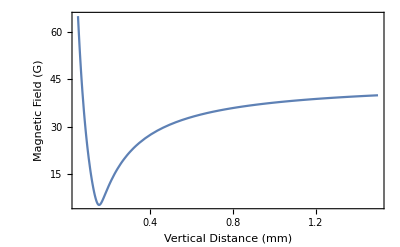
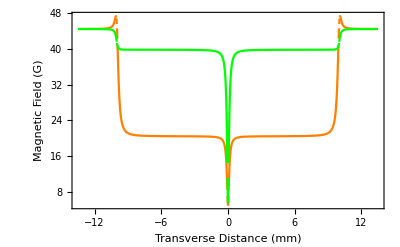
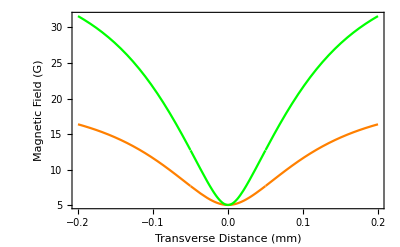

```mathematica
<<PhysicalConstants`
t=.;
Kilogram=Meter=Joule =Second=Kelvin=1;
T = 18*10^-9; (* Temperature in K *)
fc = 0.5; (* fraction of condensed atoms *)

m =87*ProtonMass;
a=104.5*BohrRadius; (* scattering length *)
hbar=PlanckConstantReduced;
kb = BoltzmannConstant;

μm=10^-6;
k=10^-7;
mA=mm=10^-3;
μ0=4π 10^-7;

(* Function FatXwire calculates the magnetic field at position (x0,y0,z0) of a rectangular conductor with finite width 2*hw.  We assume: (1) Current flows in the x direction from x1 -> x2; (2) The conductor is centered at y=yc and has width 2*hw; (3) The conductor lies entirely in the x-y plane (i.e. z=0). *)
FatXwire[x0_,y0_,z0_,hw_,yc_,x1_,x2_]:=Module[{dx1,dx2,dyPlus,dyMinus},
dx1=-x0+x1;
dx2=-x0+x2;
dyPlus=hw-y0+yc;
dyMinus=hw+y0-yc;
Return[10^-3/(2hw){0,ArcTan[(dx1 dyMinus)/(z0 √(dx1^2+dyMinus^2+z0^2))]-ArcTan[(dx2 dyMinus)/(z0 √(dx2^2+dyMinus^2+z0^2))]+ArcTan[(dx1 dyPlus)/(z0 √(dx1^2+dyPlus^2+z0^2))]-ArcTan[(dx2 dyPlus)/(z0 √(dx2^2+dyPlus^2+z0^2))],Log[(dx1+√(dx1^2+dyMinus^2+z0^2))/(dx2+√(dx2^2+dyMinus^2+z0^2))(dx2+√(dx2^2+dyPlus^2+z0^2))/(dx1+√(dx1^2+dyPlus^2+z0^2))]}];
];

(* Function FatYwire calculates the B-field at position (x0,y0,z0) for a conductor of width 2*hw at position x=xc running a finite length in y from y1->y2. We assume the conductor lies in the plane z=0. *)
FatYwire[x0_,y0_,z0_,hw_,xc_,y1_,y2_]:=Module[{dxPlus,dxMinus,dy1,dy2},
dxPlus=hw+x0-xc;
dxMinus=hw-x0+xc;
dy1=y0-y1;
dy2=-y0+y2;
Return[10^-3/(2 hw){(ArcTan[(dxPlus dy1)/(z0 √(dxPlus^2+dy1^2+z0^2))]+ArcTan[(dxMinus dy1)/(z0 √(dxMinus^2+dy1^2+z0^2))]+ArcTan[(dxPlus dy2)/(z0 √(dxPlus^2+dy2^2+z0^2))]+ArcTan[(dxMinus dy2)/(z0 √(dxMinus^2+dy2^2+z0^2))]),0,-Log[(-dy1+√(dxPlus^2+dy1^2+z0^2))/(-dy1+√(dxMinus^2+dy1^2+z0^2))(dy2+√(dxMinus^2+dy2^2+z0^2))/(dy2+√(dxPlus^2+dy2^2+z0^2))]}];
];
(* Pick a coordinate system: "x" is the direction of the main chip wire, and "y" is the direction current flows along the dimple. *)
ChipTrapField[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=Module[{VecField},
VecField=Ix*FatXwire[x,y,z,50μm,0,-10mm,+10mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-10mm,-10mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,10mm,0mm,10mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-10mm,10mm]+{Bx,By,0}; (* dimple wire *)
Return[Sqrt[VecField.VecField]]
]

z0[Ix_,Iy_,Bx_,By_]:=NMinimize[{ChipTrapField[x,y,z,Ix,Iy,Bx,By],-0.5mm<x<0.5mm,-0.5mm<y<0.5mm,2000μm>z>3μm},{x,y,z}][[2]]

μB =9.27*10^-24; (* J/T *) (* Put correct value for Rb! *)

mRb = 1.443*10^-25; (* kg *)
Dxx[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{x,2}];
Dxy[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],x,y];
Dxz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],x,z];
Dyy[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{y,2}];
Dyz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],y,z];
Dzz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{z,2}];
DMatrix[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=({{Dxx[x,y,z,Ix,Iy,Bx,By], Dxy[x,y,z,Ix,Iy,Bx,By], Dxz[x,y,z,Ix,Iy,Bx,By]}, {Dxy[x,y,z,Ix,Iy,Bx,By], Dyy[x,y,z,Ix,Iy,Bx,By], Dyz[x,y,z,Ix,Iy,Bx,By]}, {Dxz[x,y,z,Ix,Iy,Bx,By], Dyz[x,y,z,Ix,Iy,Bx,By], Dzz[x,y,z,Ix,Iy,Bx,By]}});

(* The funciton ChipTrapFrequencies calculates the position z0 where the trap is centered. It does this using the values for the chip currents and bias fields. It assumes the trap is centered at x=0 and y=0 *)
ChipTrapFrequencies[Ix_,Iy_,Bx_,By_]:= Module[{x,y,z,DMatrixDiag,xmin,ymin,zmin},
{xmin,ymin,zmin}=z0[Ix,Iy,Bx,By];
xmin=xmin[[2]];
ymin=ymin[[2]];
zmin=zmin[[2]];
DMatrixDiag=Eigensystem[DMatrix[x,y,z,Ix,Iy,Bx,By]/.{x->xmin,y->ymin,z->zmin}];
Return[
 Sqrt[μB Abs[DMatrixDiag[[1]]]/mRb]/(2π) (* in Hz *)
]
]

A=1; (* Scaling factor for the chip currents *)
CLg1=-3.25*A; (* main Z-wire current; flows in x direction in these coordinates, z direction in cart coordinates *)
CLd1=1.23*A*1;(* dimple wire current; flows in y direction in these coordinates, x direction in cart coordinates *)
Bx1=-0.90*22.6*1*A;  (* Bias field in x direction (these coordinates) or z direction (cart coordinates *)
By1=-1.75*22.6*1*A; (* Bias field in y direction (these coordinates) or x direction (cart coordinates *)

Print["Trap center (m):"]
{x1,y1,z1}=z0[CLg1,CLd1,Bx1,By1]
x1=x1[[2]];
y1=y1[[2]];
z1=z1[[2]];

Bmin1=ChipTrapField[x1,y1,z1,CLg1,CLd1,Bx1,By1];
Depth1=ChipTrapField[x1,y1,1,CLg1,CLd1,Bx1,By1]-Bmin1;
Print["Trap frequencies (Hz):"]
freqs1=ChipTrapFrequencies[CLg1,CLd1,Bx1,By1]
(*

Print["Level of cubic anharmonicity for the vertical field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[1]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,2}]
Print["Level of cubic anharmonicity for the horizontal field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[2]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,2}]


*)
Plot1=Plot[ChipTrapField[x1,y1,z mm,CLg1,CLd1,Bx1,By1],{z,0.05,1.5},
Frame->True,Axes->False,
FrameLabel->{"Vertical Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400
];
Plot2=Plot[{ChipTrapField[x mm,y1,z1,CLg1,CLd1,Bx1,By1],ChipTrapField[x1,x mm,z1,CLg1,CLd1,Bx1,By1]},{x,-13.5,13.5},PlotStyle->{Orange,Green},
Frame->True,Axes->False,
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400
];
Plot3=Plot[{ChipTrapField[x mm,y1,z1,CLg1,CLd1,Bx1,By1],ChipTrapField[x1,x mm,z1,CLg1,CLd1,Bx1,By1]},{x,-.2,.2},PlotStyle->{Orange,Green},
Frame->True,Axes->False,
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400
];
{Plot1, Plot2, Plot3}
(*Ldist=10;
dplot3d=Plot3D[ChipTrapField[x mm,y mm,z1,CLg1,CLd1,Bx1,By1],{x,-Ldist,Ldist},{y,-Ldist/10,Ldist/10},AxesLabel->{"x (mm)", "y (mm)","B(G)     "},LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14,Background->None],PlotLabel->"Magnetic field of the initial trap",PlotTheme->"Web",ImageSize->500,PlotPoints->50,PlotRange->All]
*)
```

```mathematica
<<PhysicalConstants`
t=.;
Kilogram=Meter=Joule =Second=Kelvin=1;
T = 18*10^-9; (* Temperature in K *)

Ntot=20000;
fc = 0.5; (* fraction of condensed atoms *)
T=(ω[[1]]*ω[[2]]*ω[[3]])^(1/3)*0.94*Ntot^(1/3)(PlanckConstantReduced/BoltzmannConstant)*(1-fc)^(1/3); (* Temperature in K *)
Print["Initial temperature: ", T*10^9, " nK"]



m =87*ProtonMass;
a=104.5*BohrRadius; (* scattering length *)
hbar=PlanckConstantReduced;
kb = BoltzmannConstant;

ω=2π*freqs1; (* Trap frequencies *)
Print["Omega bar:"]
ωbar=(∏_(i=1)^3 ω[[i]])^(1/3)
Print["Number of atoms in the trap:"]
Na = ((kb*T)/(0.94*hbar*ωbar))^3/(1-fc) (* Number of atoms in the trap *)
Print["Size of the thermal cloud:"]
σ=√((kb*T)/(m*ω^2))

(* delta-kick cooling*)
dkkt=0.1; (* moment of the delta kick in sec*)
dkkd = 0.00125;(* 1/2 duration of the delta kick in sec *)

A=0.0000003; (* Scaling factor for the chip currents *)
CLg1=-3.25*A; (* main Z-wire current; flows in x direction in these coordinates, z direction in cart coordinates *)
CLd1=1.23*A*1;(* dimple wire current; flows in y direction in these coordinates, x direction in cart coordinates *)
Bx1=-0.90*22.6*1*A;  (* Bias field in x direction (these coordinates) or z direction (cart coordinates *)
By1=-1.75*22.6*1*A; (* Bias field in y direction (these coordinates) or x direction (cart coordinates *)

Print["Trap center:"]
{x1,y1,z1}=z0[CLg1,CLd1,Bx1,By1]
x1=x1[[2]]; y1=y1[[2]]; z1=z1[[2]];
ωdkk=2π*ChipTrapFrequencies[CLg1,CLd1,Bx1,By1];
Print["Trap frequencies (Hz):"]
fs=ChipTrapFrequencies[CLg1,CLd1,Bx1,By1]
Print["f bar: ", (∏_(i=1)^3 fs[[i]])^(1/3) ," Hz"]


newfield[x_,y_,z_]:=10^-4 ChipTrapField[x1+z,y1+y,z1+x,CLg1,CLd1,Bx1,By1]*UnitStep[x+z1];
newfield[x_,y_,z_]:=10^-4 ChipTrapField[x1+z,y1+y,z1+x,CLg1,CLd1,Bx1,By1];

(*
Ldist=0.00005;
Lz=0.002;
Npoints=10;
Npointsz=20;
aax=D[newfield[xx,y,z],xx]/.xx->x;
DBx=Flatten[ParallelTable[{{x,y,z},aax},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
aay=D[newfield[x,yy,z],yy]/.yy->y;
DBy=Flatten[ParallelTable[{{x,y,z},aay},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
aaz=D[newfield[x,y,zz],zz]/.zz->z;
DBz=Flatten[ParallelTable[{{x,y,z},aaz},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
forceB[x_,y_,z_]=-μB*{Interpolation[DBx][x,y,z],Interpolation[DBy][x,y,z],Interpolation[DBz][x,y,z]};
*)

ωt[t_]:=ωdkk*(ⅇ^(-(t-dkkt)^2/(2 dkkd^2)));
(*ωt[t_]:=ωdkk*UnitBox[(t-dkkt)/(2dkkd)];*)


Print["Level of cubic anharmonicity for the vertical field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[1]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,2}]
Print["Level of cubic anharmonicity for the horizontal field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[2]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,2}]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Initial temperature: 909.432 nK

Omega bar:

5879.18

Number of atoms in the trap:

20000.

Size of the thermal cloud:

{9.56427×10^-7,9.82381×10^-7,4.19782×10^-6}

Trap center:

{x→-1.08741×10^-10,y→5.66565×10^-11,z→0.000151911}

Trap frequencies (Hz):

{0.846638,0.824269,0.192897}

f bar: 0.512504 Hz

Level of cubic anharmonicity for the vertical field strength (should be <<1):

-1.13589

Level of cubic anharmonicity for the horizontal field strength (should be <<1):

-3.12964×10^-6

```mathematica
order=3;
forceB[x_,y_,z_]=-μB*{D[Normal[Series[newfield[x,0,0],{x,0,order}]],x],D[Normal[Series[newfield[0,y,0],{y,0,order}]],y],D[Normal[Series[newfield[0,0,z],{z,0,order}]],z]}
{Coefficient[%[[1]],x],Coefficient[%[[2]],y],Coefficient[%[[3]],z]}
-m ωdkk^2
```

{-9.27×10^-24 (7.56435×10^-12+0.440495 x-7847.21 x^2),-9.27×10^-24 (4.14553×10^-12+0.353108 y-0.0168738 y^2),-9.27×10^-24 (-1.22778×10^-12+0.0872852 z+0.00205994 z^2)}

{-4.08339×10^-24,-3.27332×10^-24,-8.09133×10^-25}

{-4.11786×10^-24,-3.90315×10^-24,-2.13761×10^-25}

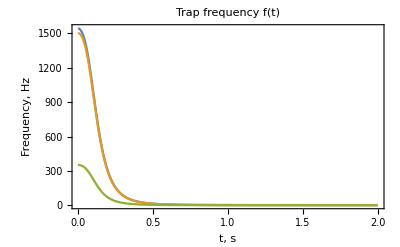

/Users/tigrank/Dropbox/CAL/TrapFreq.png

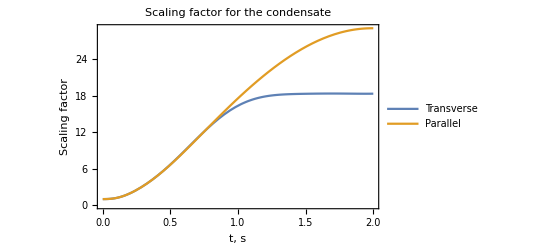

/Users/tigrank/Dropbox/CAL/Lcondplot.png

Initial trap frequencies: 2π x {1545.74,1504.9,352.18} Hz

Final trap frequencies: 2π x {0.846638,0.824269,0.192897} Hz

3.22016

Final chemical potential: 61.1969 pK

```mathematica
fullT = 2;

ωt[t_]:=(((ω+ωdkk)/2)+((ωdkk-ω)/2)Tanh[5.8(2(t/fullT)^(1/4)-1)]/Tanh[5.8])(**HeavisideTheta[.5-t]*);


Plot[Evaluate[ωt[t]/(2π)],{t, 0,fullT},PlotRange->All, Frame->True,
PlotLabel->"Trap frequency f(t)",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],FrameLabel->{"t, s", "Frequency, Hz"}]

Export[NotebookDirectory[]<>"TrapFreq.png",%,ImageResolution->300]

λ[t_]={Subscript[λ, 1][t],Subscript[λ, 2][t],Subscript[λ, 3][t]};
sol=NDSolve[{Table[λ''[t][[j]]==ω[[j]]^2/(λ[t][[1]]λ[t][[2]]λ[t][[3]]λ[t][[j]])-(ωt[t][[j]])^2 λ[t][[j]],{j,1,3}],
λ[0]=={1,1,1},λ'[0]=={0,0,0}},λ[t],{t,0,fullT}];
λcondplot=Plot[{(λ[t]/.sol)[[1, 1]], (λ[t]/.sol)[[1, 3]]},{t,0,fullT},FrameLabel->{"t, s", "Scaling factor"},Frame->True, PlotLabel->"Scaling factor for the condensate",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,PlotLegends->Placed[{"Transverse","Parallel"},{Right, Bottom}],
ImageSize->400]
Export[NotebookDirectory[]<>"Lcondplot.png",%,ImageResolution->300]
Print["Initial trap frequencies: 2π x ",ω/(2π), " Hz"]
Print["Final trap frequencies: 2π x ",ωdkk/(2π), " Hz"]

ωdkkbar=(ωdkk[[1]]*ωdkk[[2]]*ωdkk[[3]])^(1/3);
μ = (PlanckConstantReduced*ωdkkbar)/2(15*Ntot*fc*a*Sqrt[(m*ωdkkbar)/PlanckConstantReduced])^(2/5);
Print["Final chemical potential: ", μ*7.24*10^(22+12), " pK"]
```

#### Here we simulate one atom in 1D harmonic potential with 4-th order Runge-Kutta

{{{9.56427×10^-7,9.82381×10^-7,4.19782×10^-6},{0.00758443,0.00758443,0.00758443}}}

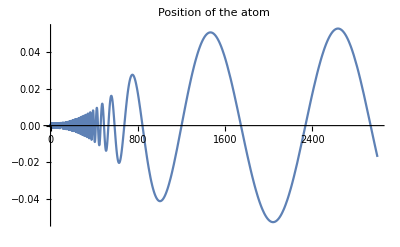

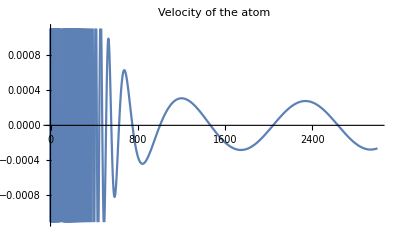

```mathematica
CRK4[]["Step"[rhs_,h_,t_,x_,xp_]]:=Module[{k0,k1,k2,k3},
k0=h xp;
k1=h rhs[t+h/2,x+k0/2];
k2=h rhs[t+h/2,x+k1/2];
k3=h rhs[t+h,x+k2];
(k0+2 k1+2 k2+k3)/6]
CRK4[___]["StepInput"]={"Function"["Time","DependentVariables"],"TimeStep","Time","DependentVariables","TemporalDerivatives"};
CRK4[___]["StepOutput"]="DependentVariablesIncrement";
CRK4[___]["DifferenceOrder"]:=4;
CRK4[___]["StepMode"]:=Fixed

SeedRandom[0]
nAtoms=1;
(* Random positions and velocities, according to Maxwell-Boltzmann *)
atoms=Transpose[{Transpose[RandomReal[NormalDistribution[0,#],nAtoms]&/@σ],RandomReal[NormalDistribution[0,Sqrt[kb*T/m]],{nAtoms,3}]}];
(* position at the radius of the cloud and "typical" velocities *)
vp=Sqrt[2*kb*T/(3m)];
atoms = {{σ, {vp,vp,vp}}}
t0=10^-3; (* Unit of time in s *)
Time=fullT*1000;
(* _____ TEST _____ *)
Time=3*1000;

(*sol=NDSolve[{x'[t]==v[t],v'[t]==-(ωt[t/1000]/1000)^2[[1]]*x[t],x[0]==atoms[[1, 1, 1]],v[0]==atoms[[1, 2, 1]]/1000},{x,v},{t,0,Time},Method->CRK4];*)
(* Here we measure distances in mm and time in ms to reduce the numerical error *)
sol=NDSolve[{x'[t]==v[t],v'[t]==-((ωt[t/1000]/1000)^2)[[1]]*x[t],x[0]==atoms[[1, 1, 1]]*1000,v[0]==atoms[[1, 2, 1]]},{x,v},{t,0,Time},Method->CRK4];
Plot[{x[t]/.sol},{t, 0,Time}, PlotLabel->"Position of the atom"]
Plot[{v[t]/.sol},{t, 0,Time}, PlotLabel->"Velocity of the atom"]
```

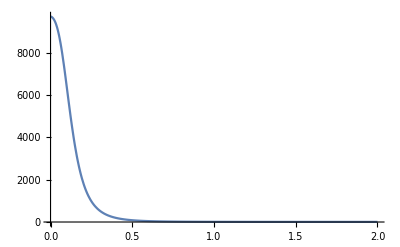

```mathematica
Plot[(ωt[t])[[1]],{t, 0,Time/1000},PlotRange->All]
```

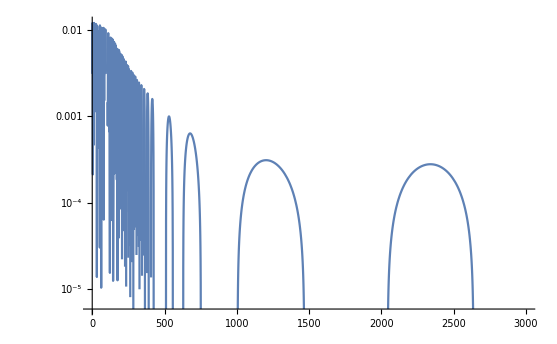

```mathematica
LogPlot[{v[t]/.sol},{t, 0,Time}]
```

#### Here we test the situation with a static trap to see the contribution of the numerical error (computer friction)

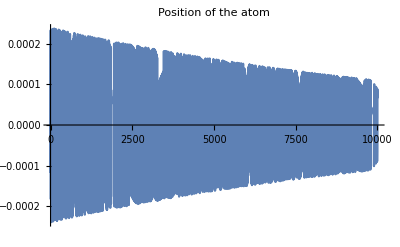

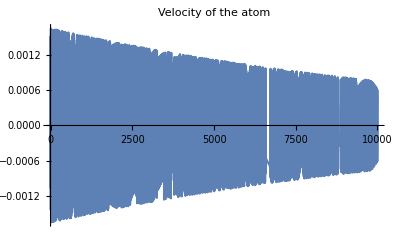

```mathematica
ωt[t_]:=ω
sol=NDSolve[{x'[t]==v[t],v'[t]==-((ωt[t/1000]/1000)^2)[[1]]*x[t],x[0]==atoms[[1, 1, 1]]*1000,v[0]==atoms[[1, 2, 1]]},{x,v},{t,0,Time},Method->CRK4];
Plot[{x[t]/.sol},{t, 0,Time}, PlotLabel->"Position of the atom"]
Plot[{v[t]/.sol},{t, 0,Time}, PlotLabel->"Velocity of the atom"]
```

OK, it is approximately linear, but depends on velocity. For the initial position, the slope is described by change 6/24=0.25 per 10s. For the velocity: 5/16=0.3

```mathematica
(* Envelope function to find square of oscillation amplitudes *)

FunctionEnvelope[f_,{t_,a_,b_},n_: 40]:=Module[{seeds,x,y,points,progress=0,tempf,union},seeds=Rescale[Range[0,1,1/n]+1/(2 n),{0,1},{a,b}];
points=Last[Last[Reap[Monitor[Do[Quiet@Check[progress++;{y,x}=FindMaximum[Abs[f],{t,x0}];
x=t/.x;If[a≤x≤b,Sow[{x,y}]],Null],{x0,seeds}],ProgressIndicator[progress,{0,Length[seeds]}]]]]];
union[]:=points=Union[points,SameTest->(Abs[First[#1]-First[#2]]/Replace[Max[Abs[First[#1]],Abs[First[#2]]],u_/;u==0:>1]<10^-6&)];
union[];
tempf=Interpolation[points, InterpolationOrder->1];
points=Quiet[Join[{{a,tempf[a]}},points,{{b,tempf[b]}}]];
union[];
Interpolation[points, InterpolationOrder->1]]
```

```mathematica
g=FunctionEnvelope[(v[t]/v[0])^2/.sol,{t,0,Time},200];
```

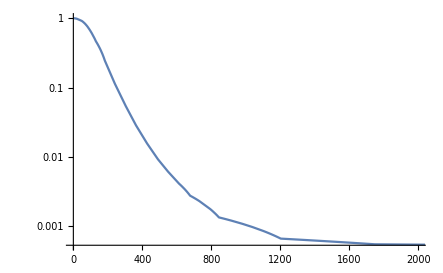

```mathematica
LogPlot[g[t]/g[0],{t,0,Time},PlotRange->{{0,fullT*1000},All}]
```

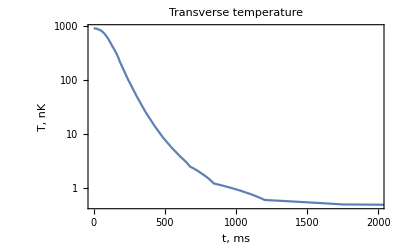

/Users/tigrank/Dropbox/CAL/trTPlot.png

```mathematica
(* Plotting the trasverse temperature, taking into account computer friction *)
trTPlot=LogPlot[T*10^9*g[t]/g[0](*/(1+g[t]/g[0] t/Time*(0.3-1))*),{t,0,Time},PlotRange->{{0, fullT*1000}, All},FrameLabel->{"t, ms", "T, nK"},Frame->True, PlotLabel->"Transverse temperature",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400,LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None]]
Export[NotebookDirectory[]<>"trTPlot.png",%,ImageResolution->300]
```

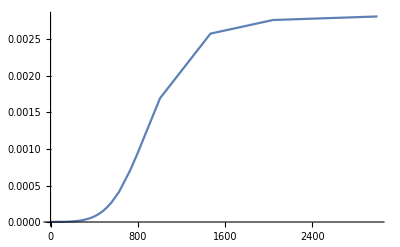

```mathematica
g=FunctionEnvelope[(x[t])^2/.sol,{t,0,Time},400];
Plot[g[t],{t,0,Time},PlotRange->All]
```

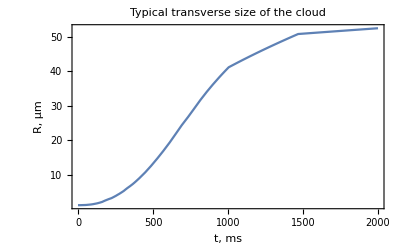

/Users/tigrank/Dropbox/CAL/trRPlot.png

```mathematica
trRPlot=Plot[10^3 Sqrt[g[t]],{t,0,Time},PlotRange->All,FrameLabel->{"t, ms", "R, μm"},PlotRange->{{0,fullT*1000}, All},Frame->True, PlotLabel->"Typical transverse size of the cloud",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400]
Export[NotebookDirectory[]<>"trRPlot.png",%,ImageResolution->300]
```

```mathematica
FunctionEnvelope[f_,{t_,a_,b_},n_: 40]:=Module[{seeds,x,y,points,progress=0,tempf,union},seeds=Rescale[Range[0,1,1/n]+1/(2 n),{0,1},{a,b}];
points=Last[Last[Reap[Monitor[Do[Quiet@Check[progress++;{y,x}=FindMaximum[Abs[f],{t,x0}];
x=t/.x;If[a≤x≤b,Sow[{x,y}]],Null],{x0,seeds}],ProgressIndicator[progress,{0,Length[seeds]}]]]]];
union[]:=points=Union[points,SameTest->(Abs[First[#1]-First[#2]]/Replace[Max[Abs[First[#1]],Abs[First[#2]]],u_/;u==0:>1]<10^-6&)];
union[];
tempf=Interpolation[points,  InterpolationOrder->1];
points=Quiet[Join[{{a,tempf[a]}},points,{{b,tempf[b]}}]];
union[];
Interpolation[points, InterpolationOrder->1]]
```

```mathematica
g=FunctionEnvelope[(v[t]/v[0])^2/.sol,{t,0,Time},200];
```

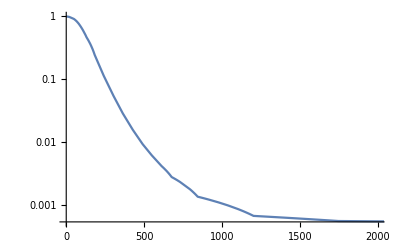

```mathematica
LogPlot[g[t]/g[0],{t,0,Time},PlotRange->{{0, 2000},All}]
```